```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];

plot[nocorrdatfile_,corrdatfile_,mminnoip_,mminip_]:=Module[{},
nocorrdata=Import[nocorrdatfile];
corrdata=Import[corrdatfile];
nocorrE=Transpose[nocorrdata][[4]];
corrE=Transpose[corrdata][[4]];
nocorrσ=Transpose[nocorrdata][[6]];
corrσ=Transpose[corrdata][[6]];

nocorrl=Length[nocorrE];
corrl=Length[corrE];
nomean=Mean[nocorrE[[mminnoip;;nocorrl]]];
ipmean=Mean[corrE[[mminip;;corrl]]];
noerr=Sqrt[Total[nocorrσ[[mminnoip;;nocorrl]]^2]/Length[nocorrσ[[mminnoip;;nocorrl]]]];
iperr=Sqrt[Total[corrσ[[mminip;;corrl]]^2]/Length[corrσ[[mminip;;corrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{{mminnoip,Red},{mminip,Blue}},{}},GridLinesStyle->Directive[Red],Frame->{{True,False},{True,False}},FrameStyle->15,FrameLabel->{"block","E (MeV)"},ImageSize->350,PlotRange->All]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{StringJoin[ToString[noerr],", noip"],StringJoin[ToString[iperr],", ip"]},GridLines->{{{mminnoip,Red},{mminip,Blue}},{}},Frame->{{True,False},{True,False}},FrameStyle->15,FrameLabel->{"block","ΔE (MeV)"},ImageSize->350,PlotRange->All]
]

plot3[nocorrdatfile_,corrdatfile_,quaddatfile_,mminnoip_,mminip_,mminquad_]:=Module[{},
nocorrdata=Import[nocorrdatfile];
corrdata=Import[corrdatfile];
quaddata=Import[quaddatfile];
nocorrE=Transpose[nocorrdata][[4]];
corrE=Transpose[corrdata][[4]];
quadE=Transpose[quaddata][[4]];
nocorrσ=Transpose[nocorrdata][[6]];
corrσ=Transpose[corrdata][[6]];
quadσ=Transpose[quaddata][[6]];

nocorrl=Length[nocorrE];
corrl=Length[corrE];
quadl=Length[quadE];
nomean=Mean[nocorrE[[mminnoip;;nocorrl]]];
ipmean=Mean[corrE[[mminip;;corrl]]];
quadmean=Mean[quadE[[mminquad;;quadl]]];
noerr=Sqrt[Total[nocorrσ[[mminnoip;;nocorrl]]^2]/Length[nocorrσ[[mminnoip;;nocorrl]]]];
iperr=Sqrt[Total[corrσ[[mminip;;corrl]]^2]/Length[corrσ[[mminip;;corrl]]]];
quaderr=Sqrt[Total[quadσ[[mminquad;;quadl]]^2]/Length[quadσ[[mminquad;;quadl]]]];

ListPlot[{nocorrE,corrE,quadE},Joined->True,PlotStyle->{{Blue},{Red},{Green}},PlotLegends->{nomean,ipmean,quadmean},GridLines->{{{mminnoip,Red},{mminip,Blue},{mminquad,Green}},{}},GridLinesStyle->Directive[Red],Frame->{{True,False},{True,False}},FrameStyle->15,FrameLabel->{"block","E (MeV)"},ImageSize->350,PlotRange->All]
ListPlot[{nocorrσ,corrσ,quadσ},Joined->True,PlotStyle->{{Blue},{Red},{Green}},PlotLegends->{StringJoin[ToString[noerr],", noip"],StringJoin[ToString[iperr],", ip"],StringJoin[ToString[quaderr],", quad"]},GridLines->{{{mminnoip,Red},{mminip,Blue},{mminquad,Green}},{}},Frame->{{True,False},{True,False}},FrameStyle->15,FrameLabel->{"block","ΔE (MeV)"},ImageSize->350,PlotRange->All]
]
```

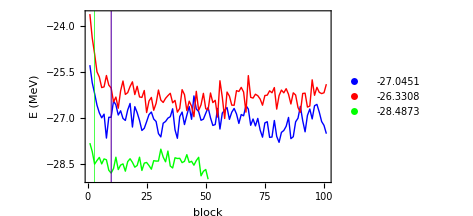
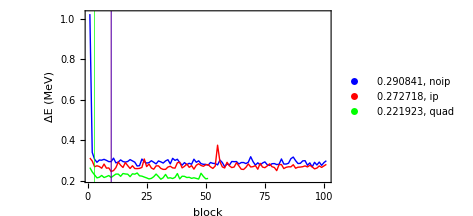

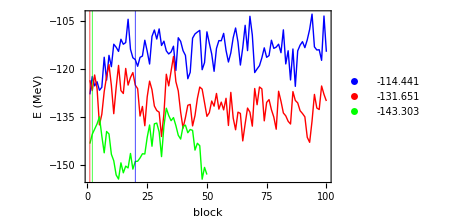
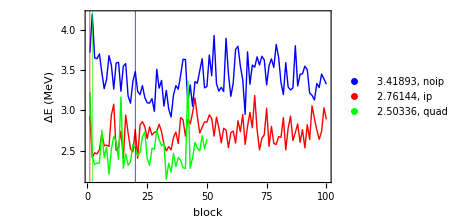

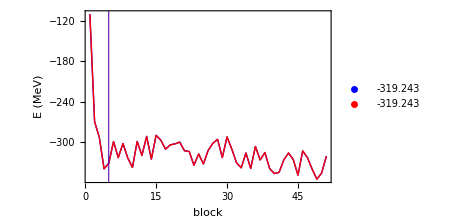
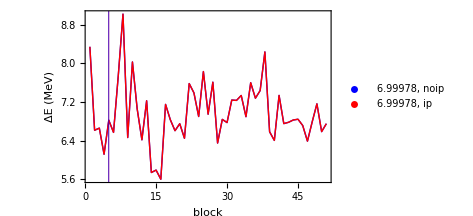

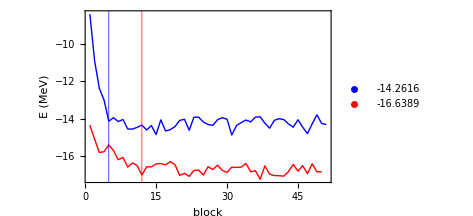
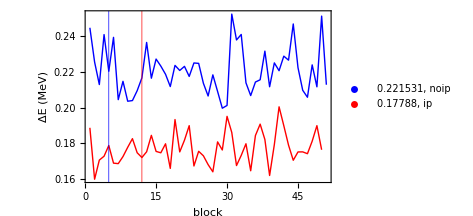

Plot3[-Graphics- -Graphics-]

```mathematica
plot3["he4noip.dat","he4ip.dat","he4quad.dat",10,10,3]
plot3["o16noip.dat","o16ip.dat","o16quad.dat",1,20,2]
plot["ca40noip.dat","ca40noip.dat",5,5]
plot["nucmatnoip.dat","nucmatip.dat",12,5]
plot["he4noip.dat","newdmc10000quad.dat",5,5]
Plot3[plot3["he4noip.dat","he4ip.dat","he4dmctest.dat",10,10,3]]
```

```mathematica
datano=Import["o16noip.dat"];
dataip=Import["o16ip.dat"];
dataquad=Import["o16quad.dat"];

datano=Transpose[datano][[4]][[1;;Length[datano]]];
dataip=Transpose[dataip][[4]][[20;;Length[dataip]]];
dataquad=Transpose[dataquad][[4]][[2;;Length[dataquad]]];

Mean[datano]+15
Mean[dataip]+15
Mean[dataquad]+15
StandardDeviation[datano]
StandardDeviation[dataip]
StandardDeviation[dataquad]
```

-99.441

-116.651

-128.303

5.21889

5.08242

6.02438